```mathematica
(* Pie chart in Fig 1D *)
(* Sevahn Vorperian, Quake Lab *)
```

```mathematica
fractions = Import["/Users/kayaneh/Documents/deconvolution/revision1/08012021_perComp_noEye_sigmat_18/adnci_v18_rmseAll_11282021/BioIVT_sigMat18_avgCoefs_plasma_1129021.csv"];
fractions = Import["/Users/kayaneh/Documents/deconvolution/projectcode/fig1/BioIVT_sigMat18_avgCoefs_plasma.csv"];
```

```mathematica
roundPower = 0.1;
percentThresh = 1; (* percentage cutoff for stacked bar chart vs main pie *)
scalePercents = 100; (* scale all percentages by 100 *)
superSmallThresh = 0.1; (* percentage cutoff for cell types with small fractional contirbutions *)
sampleCenter = "BioIVT";
```

```mathematica
fractions
```

{{,BioIVT},{platelet,0.336043},{erythrocyte/erythroid progenitor,0.265095},{monocyte,0.0564103},{b cell,0.0403988},{nk cell,0.0369114},{neutrophil,0.0330109},{endothelial cell,0.0260076},{mature conventional dendritic cell,0.0193669},{basophil,0.0184614},{intestinal tuft cell,0.0141496},{adventitial cell,0.013551},{cell of skeletal muscle,0.0134363},{salivary/bronchial secretory cell,0.0122549},{thymocyte,0.0119203},{intestinal enterocyte,0.0080684},{basal cell,0.00799628},{salivary gland cell,0.0079842},{myeloid progenitor,0.00727435},{pericyte cell,0.00694598},{respiratory ciliated cell,0.00596868},{t cell,0.00546688},{intrahepatic cholangiocyte,0.00527454},{schwann cell,0.0050337},{ionocyte/luminal epithelial cell of mammary gland,0.00489585},{pancreatic stellate cell,0.00475141},{intestinal secretory cell,0.00442965},{medullary thymic epithelial cell,0.0043699},{hematopoietic stem cell,0.00298282},{kidney epithelial cell,0.00241723},{macrophage,0.00230917},{secretory cell,0.00213823},{basal cell of prostate epithelium,0.00207947},{pancreatic alpha/beta cell,0.0018809},{type ii pneumocyte,0.00179105},{pancreatic ductal cell,0.0016609},{prostate epithelia,0.00111878},{plasmablast,0.000773699},{tendon cell,0.000732589},{respiratory secretory cell,0.000705838},{innate lymphoid cell,0.00063209},{club cell/type i pneumocyte,0.000520479},{pancreatic acinar cell,0.000425606},{mesothelial cell,0.000389906},{goblet cell,0.000343732},{pancreatic pp cell,0.000290813},{bladder urothelial cell,0.000280461},{mast cell,0.000207723},{plasma cell,0.000192536},{gland cell,0.000178261},{duodenum glandular cell,0.000175315},{melanocyte,0.000080599},{hepatocyte,0.0000535943},{fibroblast/mesenchymal stem cell,0.0000530125},{pancreatic delta cell,0.0000443203},{luminal cell of prostate epithelium,0.000041352},{stromal cell,0.0000171159},{ciliated epithelial cell/epithelial cell of uterus,5.43287×10^-6},{cardiac muscle cell,0.},{intestinal crypt stem cell,0.},{smooth muscle cell,0.},{pulmonary ionocyte,0.},{keratinocyte,0.}}

```mathematica
fractions = fractions[[2;;]]; (* eliminate the center name *)
```

```mathematica
cellTypes = fractions[[;;,1]]
```

{platelet,erythrocyte/erythroid progenitor,monocyte,b cell,nk cell,neutrophil,endothelial cell,mature conventional dendritic cell,basophil,intestinal tuft cell,adventitial cell,cell of skeletal muscle,salivary/bronchial secretory cell,thymocyte,intestinal enterocyte,basal cell,salivary gland cell,myeloid progenitor,pericyte cell,respiratory ciliated cell,t cell,intrahepatic cholangiocyte,schwann cell,ionocyte/luminal epithelial cell of mammary gland,pancreatic stellate cell,intestinal secretory cell,medullary thymic epithelial cell,hematopoietic stem cell,kidney epithelial cell,macrophage,secretory cell,basal cell of prostate epithelium,pancreatic alpha/beta cell,type ii pneumocyte,pancreatic ductal cell,prostate epithelia,plasmablast,tendon cell,respiratory secretory cell,innate lymphoid cell,club cell/type i pneumocyte,pancreatic acinar cell,mesothelial cell,goblet cell,pancreatic pp cell,bladder urothelial cell,mast cell,plasma cell,gland cell,duodenum glandular cell,melanocyte,hepatocyte,fibroblast/mesenchymal stem cell,pancreatic delta cell,luminal cell of prostate epithelium,stromal cell,ciliated epithelial cell/epithelial cell of uterus,cardiac muscle cell,intestinal crypt stem cell,smooth muscle cell,pulmonary ionocyte,keratinocyte}

```mathematica
(* fractions =fractions[[2;;,2;;]][[1]] *)
fractions = fractions[[;;,2]]
```

{0.336043,0.265095,0.0564103,0.0403988,0.0369114,0.0330109,0.0260076,0.0193669,0.0184614,0.0141496,0.013551,0.0134363,0.0122549,0.0119203,0.0080684,0.00799628,0.0079842,0.00727435,0.00694598,0.00596868,0.00546688,0.00527454,0.0050337,0.00489585,0.00475141,0.00442965,0.0043699,0.00298282,0.00241723,0.00230917,0.00213823,0.00207947,0.0018809,0.00179105,0.0016609,0.00111878,0.000773699,0.000732589,0.000705838,0.00063209,0.000520479,0.000425606,0.000389906,0.000343732,0.000290813,0.000280461,0.000207723,0.000192536,0.000178261,0.000175315,0.000080599,0.0000535943,0.0000530125,0.0000443203,0.000041352,0.0000171159,5.43287×10^-6,0.,0.,0.,0.,0.}

```mathematica
(* fractions = Import["~/Documents/deconvolution/cellTypeFractions_10XDecon_07222020.xlsx"][[1]]; *)
```

```mathematica
contribs = fractions  (* excluded sample name and r, p-value, RMSE *)
```

{0.336043,0.265095,0.0564103,0.0403988,0.0369114,0.0330109,0.0260076,0.0193669,0.0184614,0.0141496,0.013551,0.0134363,0.0122549,0.0119203,0.0080684,0.00799628,0.0079842,0.00727435,0.00694598,0.00596868,0.00546688,0.00527454,0.0050337,0.00489585,0.00475141,0.00442965,0.0043699,0.00298282,0.00241723,0.00230917,0.00213823,0.00207947,0.0018809,0.00179105,0.0016609,0.00111878,0.000773699,0.000732589,0.000705838,0.00063209,0.000520479,0.000425606,0.000389906,0.000343732,0.000290813,0.000280461,0.000207723,0.000192536,0.000178261,0.000175315,0.000080599,0.0000535943,0.0000530125,0.0000443203,0.000041352,0.0000171159,5.43287×10^-6,0.,0.,0.,0.,0.}

```mathematica
Length[fractions]
```

62

```mathematica
Length[cellTypes]
```

62

```mathematica
(* first get the zero index *)
```

```mathematica
zeroIndex = Position[contribs, val_/;val ≤ 0]
```

{{58},{59},{60},{61},{62}}

```mathematica
(* drop it from the contributions and drop the corresponding labels *)
```

```mathematica
nonZeroVals = Delete[contribs, zeroIndex];
```

```mathematica
nonZeroVals = nonZeroVals * scalePercents
```

{33.6043,26.5095,5.64103,4.03988,3.69114,3.30109,2.60076,1.93669,1.84614,1.41496,1.3551,1.34363,1.22549,1.19203,0.80684,0.799628,0.79842,0.727435,0.694598,0.596868,0.546688,0.527454,0.50337,0.489585,0.475141,0.442965,0.43699,0.298282,0.241723,0.230917,0.213823,0.207947,0.18809,0.179105,0.16609,0.111878,0.0773699,0.0732589,0.0705838,0.063209,0.0520479,0.0425606,0.0389906,0.0343732,0.0290813,0.0280461,0.0207723,0.0192536,0.0178261,0.0175315,0.0080599,0.00535943,0.00530125,0.00443203,0.0041352,0.00171159,0.000543287}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
nonZeroCells = Delete[cellTypes, zeroIndex];
```

```mathematica
Length[nonZeroCells]
```

57

```mathematica
nonZeroCells
```

{platelet,erythrocyte/erythroid progenitor,monocyte,b cell,nk cell,neutrophil,endothelial cell,mature conventional dendritic cell,basophil,intestinal tuft cell,adventitial cell,cell of skeletal muscle,salivary/bronchial secretory cell,thymocyte,intestinal enterocyte,basal cell,salivary gland cell,myeloid progenitor,pericyte cell,respiratory ciliated cell,t cell,intrahepatic cholangiocyte,schwann cell,ionocyte/luminal epithelial cell of mammary gland,pancreatic stellate cell,intestinal secretory cell,medullary thymic epithelial cell,hematopoietic stem cell,kidney epithelial cell,macrophage,secretory cell,basal cell of prostate epithelium,pancreatic alpha/beta cell,type ii pneumocyte,pancreatic ductal cell,prostate epithelia,plasmablast,tendon cell,respiratory secretory cell,innate lymphoid cell,club cell/type i pneumocyte,pancreatic acinar cell,mesothelial cell,goblet cell,pancreatic pp cell,bladder urothelial cell,mast cell,plasma cell,gland cell,duodenum glandular cell,melanocyte,hepatocyte,fibroblast/mesenchymal stem cell,pancreatic delta cell,luminal cell of prostate epithelium,stromal cell,ciliated epithelial cell/epithelial cell of uterus}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
(* get index cell types that are less than one percent together for the bar chart *)
```

```mathematica
lt1Percent = Position[nonZeroVals, val_/;val  < percentThresh]
```

{{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57}}

```mathematica
(* now pull the cell types and their associated values and put in reverse order so it goes from smallest to largest *)
```

```mathematica
smallContribVals = Reverse[Part[nonZeroVals, # ]&/@ lt1Percent]
smallContribCells = Reverse[Part[nonZeroCells, #] &/@ lt1Percent];
```

{{0.000543287},{0.00171159},{0.0041352},{0.00443203},{0.00530125},{0.00535943},{0.0080599},{0.0175315},{0.0178261},{0.0192536},{0.0207723},{0.0280461},{0.0290813},{0.0343732},{0.0389906},{0.0425606},{0.0520479},{0.063209},{0.0705838},{0.0732589},{0.0773699},{0.111878},{0.16609},{0.179105},{0.18809},{0.207947},{0.213823},{0.230917},{0.241723},{0.298282},{0.43699},{0.442965},{0.475141},{0.489585},{0.50337},{0.527454},{0.546688},{0.596868},{0.694598},{0.727435},{0.79842},{0.799628},{0.80684}}

```mathematica
(* get the indices where the elements are ≤ 0.1% or 0.001 *)
```

```mathematica
ltPt1Percent = Position[Flatten[smallContribVals], val_/;val  ≤ superSmallThresh]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21}}

```mathematica
(* get the sum of the values and the respective cell ≤ 0.1 % *)
fracsLTPt1 = Part[smallContribVals, # ] &/@ ltPt1Percent
cellsLTPt1 = Part[smallContribCells, #] &/@ ltPt1Percent
```

{{{0.000543287}},{{0.00171159}},{{0.0041352}},{{0.00443203}},{{0.00530125}},{{0.00535943}},{{0.0080599}},{{0.0175315}},{{0.0178261}},{{0.0192536}},{{0.0207723}},{{0.0280461}},{{0.0290813}},{{0.0343732}},{{0.0389906}},{{0.0425606}},{{0.0520479}},{{0.063209}},{{0.0705838}},{{0.0732589}},{{0.0773699}}}

{{{ciliated epithelial cell/epithelial cell of uterus}},{{stromal cell}},{{luminal cell of prostate epithelium}},{{pancreatic delta cell}},{{fibroblast/mesenchymal stem cell}},{{hepatocyte}},{{melanocyte}},{{duodenum glandular cell}},{{gland cell}},{{plasma cell}},{{mast cell}},{{bladder urothelial cell}},{{pancreatic pp cell}},{{goblet cell}},{{mesothelial cell}},{{pancreatic acinar cell}},{{club cell/type i pneumocyte}},{{innate lymphoid cell}},{{respiratory secretory cell}},{{tendon cell}},{{plasmablast}}}

```mathematica
totalSuperSmall = Total[Flatten[fracsLTPt1]]
```

0.614447

```mathematica
(* now drop those small guys *)
```

```mathematica
goodSmallVals = Delete[smallContribVals, ltPt1Percent];
goodSmallCells = Delete[smallContribCells, ltPt1Percent];
```

```mathematica
goodSmallCells
```

{{prostate epithelia},{pancreatic ductal cell},{type ii pneumocyte},{pancreatic alpha/beta cell},{basal cell of prostate epithelium},{secretory cell},{macrophage},{kidney epithelial cell},{hematopoietic stem cell},{medullary thymic epithelial cell},{intestinal secretory cell},{pancreatic stellate cell},{ionocyte/luminal epithelial cell of mammary gland},{schwann cell},{intrahepatic cholangiocyte},{t cell},{respiratory ciliated cell},{pericyte cell},{myeloid progenitor},{salivary gland cell},{basal cell},{intestinal enterocyte}}

```mathematica
(* add the sum of the remaining cells *)
goodSmallVals = AppendTo[goodSmallVals, {totalSuperSmall}]
goodSmallCells = AppendTo[goodSmallCells, {"Very Small Contributors"}]
```

{{0.111878},{0.16609},{0.179105},{0.18809},{0.207947},{0.213823},{0.230917},{0.241723},{0.298282},{0.43699},{0.442965},{0.475141},{0.489585},{0.50337},{0.527454},{0.546688},{0.596868},{0.694598},{0.727435},{0.79842},{0.799628},{0.80684},{0.614447}}

{{prostate epithelia},{pancreatic ductal cell},{type ii pneumocyte},{pancreatic alpha/beta cell},{basal cell of prostate epithelium},{secretory cell},{macrophage},{kidney epithelial cell},{hematopoietic stem cell},{medullary thymic epithelial cell},{intestinal secretory cell},{pancreatic stellate cell},{ionocyte/luminal epithelial cell of mammary gland},{schwann cell},{intrahepatic cholangiocyte},{t cell},{respiratory ciliated cell},{pericyte cell},{myeloid progenitor},{salivary gland cell},{basal cell},{intestinal enterocyte},{Very Small Contributors}}

```mathematica
(* now sort this finalized "small cell" list *)
```

```mathematica
finalOrder = Reverse[Ordering[goodSmallVals]]
```

{22,21,20,19,18,23,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
goodSmallVals = Flatten[Part[goodSmallVals , #] &/@ finalOrder]
```

{0.80684,0.799628,0.79842,0.727435,0.694598,0.614447,0.596868,0.546688,0.527454,0.50337,0.489585,0.475141,0.442965,0.43699,0.298282,0.241723,0.230917,0.213823,0.207947,0.18809,0.179105,0.16609,0.111878}

```mathematica
goodSmallCells = Flatten[Part[goodSmallCells, #] &/@ finalOrder]
```

{intestinal enterocyte,basal cell,salivary gland cell,myeloid progenitor,pericyte cell,Very Small Contributors,respiratory ciliated cell,t cell,intrahepatic cholangiocyte,schwann cell,ionocyte/luminal epithelial cell of mammary gland,pancreatic stellate cell,intestinal secretory cell,medullary thymic epithelial cell,hematopoietic stem cell,kidney epithelial cell,macrophage,secretory cell,basal cell of prostate epithelium,pancreatic alpha/beta cell,type ii pneumocyte,pancreatic ductal cell,prostate epithelia}

```mathematica
(* now make the bar chart *)
```

```mathematica
shortlist =List[Flatten[Table[Callout[goodSmallVals[[#]], goodSmallCells[[#]],After,Appearance->"Leader",LeaderSize->{15,Automatic,2}],1] &/@Range[Length[goodSmallCells]]]];
```

```mathematica
shortlist
```

{{Callout[0.80684,intestinal enterocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.799628,basal cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.79842,salivary gland cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.727435,myeloid progenitor,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.694598,pericyte cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.614447,Very Small Contributors,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.596868,respiratory ciliated cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.546688,t cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.527454,intrahepatic cholangiocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.50337,schwann cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.489585,ionocyte/luminal epithelial cell of mammary gland,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.475141,pancreatic stellate cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.442965,intestinal secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.43699,medullary thymic epithelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.298282,hematopoietic stem cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.241723,kidney epithelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.230917,macrophage,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.213823,secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.207947,basal cell of prostate epithelium,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.18809,pancreatic alpha/beta cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.179105,type ii pneumocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.16609,pancreatic ductal cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.111878,prostate epithelia,After,Appearance→Leader,LeaderSize→{15,Automatic,2}]}}

```mathematica
piePal = Map [RGBColor,{"#bee9e8","#62b6cb","#1b4965","#cae9ff","#5fa8d3", "#f26419", "#a4508b", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab", "#5bba6f", "#9ece9a", "#c8d5b9"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313]}

```mathematica
(* would use LabelingSize function but its not available before version 11.3 
https://reference.wolfram.com/language/ref/LabelingSize.html*)
```

```mathematica
barPal = Map[RGBColor, {"#0081a7","#06BEE1","#00afb9","#61A5C2","#168AAD","#6d597a","#d62828","#f07167","#f77f00","#fcbf49","#eae2b7","#C2E7D9","#89b0ae",
 "#A9D6E5","#7EBDC2",
  "#468FAF", "#2A6F97", "#5B85AA",
  (* "#276FBF", *)"#457b9d","#6096ba",
"#414770", "#6D597A", "#b56576",(*"#E56B6F",*)"#FFBF81","#FFD9CE"}]
```

{RGBColor[0., 0.5058823529411764, 0.6549019607843137],RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],RGBColor[0., 0.6862745098039216, 0.7254901960784313],RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],RGBColor[0.9686274509803922, 0.4980392156862745, 0.],RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.2549019607843137, 0.2784313725490196, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

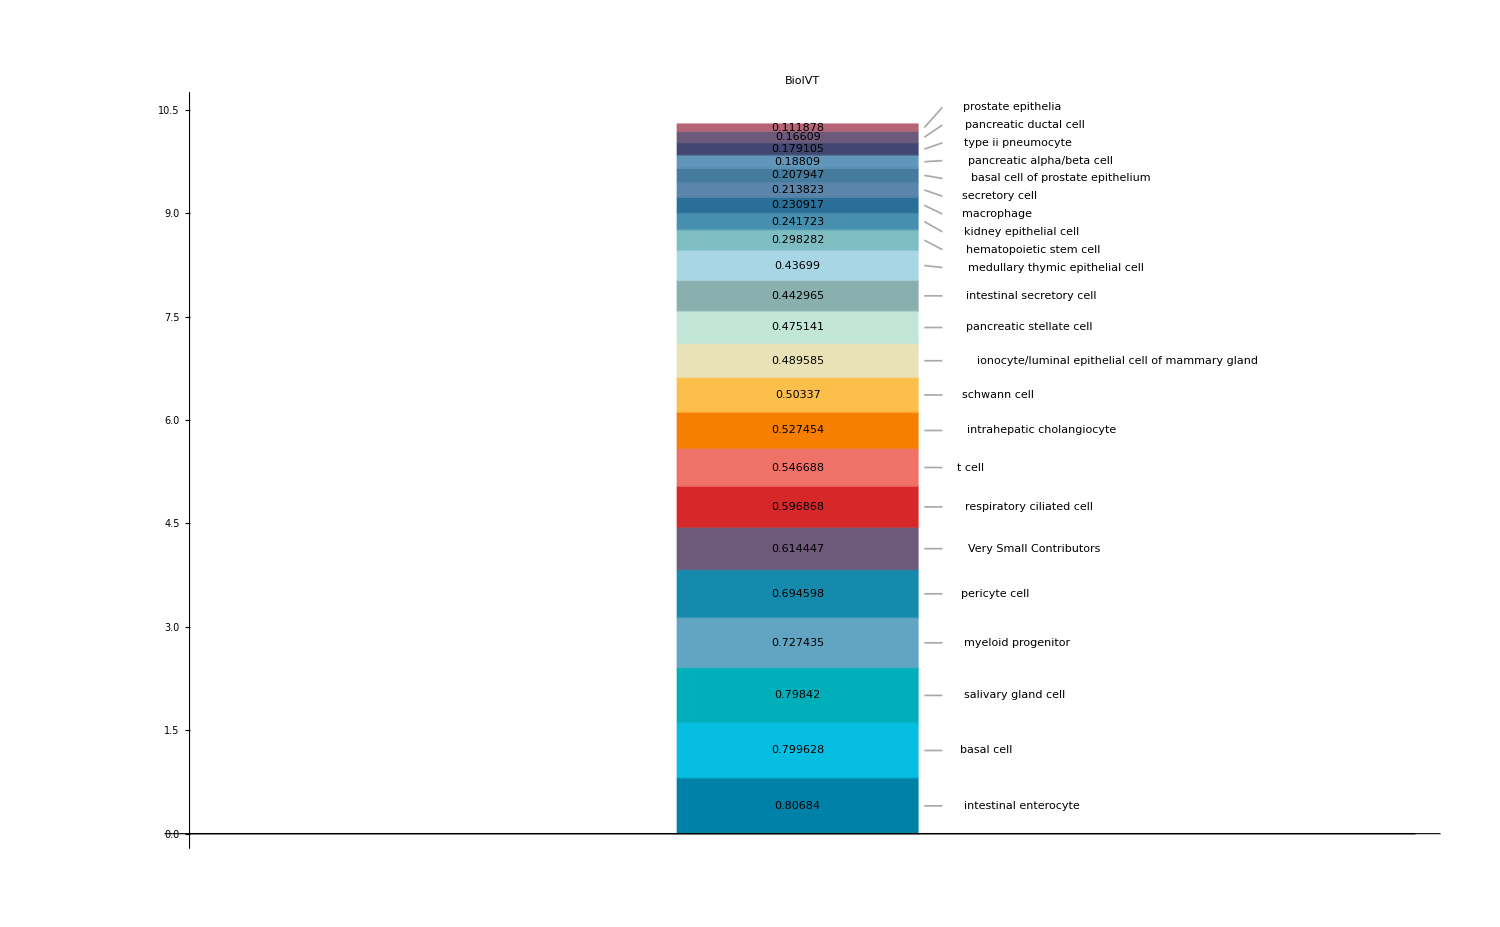

```mathematica
BarChart[shortlist,BarSpacing->2,ChartLayout->"Stacked",
ChartStyle-> barPal, ImageSize-> 1500, LabelingFunction ->( Placed[#1, Center]&), BaseStyle->{FontSize->15}, PlotLabel -> sampleCenter]
```

```mathematica
(* cool, now it's time to make the pie chart *)
```

```mathematica
gtPt1Percent = Position[Flatten[nonZeroVals], val_/;val  >=percentThresh ]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14}}

```mathematica
bigContribs = Part[nonZeroVals, #] &/@ gtPt1Percent
```

{{33.6043},{26.5095},{5.64103},{4.03988},{3.69114},{3.30109},{2.60076},{1.93669},{1.84614},{1.41496},{1.3551},{1.34363},{1.22549},{1.19203}}

```mathematica
bigCells = Part[nonZeroCells, #] &/@ gtPt1Percent
```

{{platelet},{erythrocyte/erythroid progenitor},{monocyte},{b cell},{nk cell},{neutrophil},{endothelial cell},{mature conventional dendritic cell},{basophil},{intestinal tuft cell},{adventitial cell},{cell of skeletal muscle},{salivary/bronchial secretory cell},{thymocyte}}

```mathematica
bigTot = Total[Flatten[bigContribs]] ;
smallContribTot = Total[Flatten[goodSmallVals]];
bigTot + smallContribTot (* cool, so we sum to 1 between small and big contributions *)
```

100.

```mathematica
(* add the sum of the small contributions *)
```

```mathematica
bigContribs= AppendTo[bigContribs, {smallContribTot}];
bigCells = AppendTo[bigCells, {"Small"}]
```

{{platelet},{erythrocyte/erythroid progenitor},{monocyte},{b cell},{nk cell},{neutrophil},{endothelial cell},{mature conventional dendritic cell},{basophil},{intestinal tuft cell},{adventitial cell},{cell of skeletal muscle},{salivary/bronchial secretory cell},{thymocyte},{Small}}

```mathematica
Total[Flatten[bigContribs]]
```

100.

```mathematica
(* now it's time to sort it from big to small *)
```

```mathematica
finalOrderBig = Reverse[Ordering[bigContribs]];
bigContribs = Flatten[Part[bigContribs, #] &/@ finalOrderBig];
bigCells = Flatten[Part[bigCells, #] &/@ finalOrderBig];
```

```mathematica
(* make the labels for the pie chart *)
```

```mathematica
bigContribs
```

{33.6043,26.5095,10.2983,5.64103,4.03988,3.69114,3.30109,2.60076,1.93669,1.84614,1.41496,1.3551,1.34363,1.22549,1.19203}

```mathematica
test = Callout[bigContribs[[#]], bigCells[[#]],  Appearance -> "Leader"]&/@ Range[Length[bigCells]]
```

{Callout[33.6043,platelet,Appearance→Leader],Callout[26.5095,erythrocyte/erythroid progenitor,Appearance→Leader],Callout[10.2983,Small,Appearance→Leader],Callout[5.64103,monocyte,Appearance→Leader],Callout[4.03988,b cell,Appearance→Leader],Callout[3.69114,nk cell,Appearance→Leader],Callout[3.30109,neutrophil,Appearance→Leader],Callout[2.60076,endothelial cell,Appearance→Leader],Callout[1.93669,mature conventional dendritic cell,Appearance→Leader],Callout[1.84614,basophil,Appearance→Leader],Callout[1.41496,intestinal tuft cell,Appearance→Leader],Callout[1.3551,adventitial cell,Appearance→Leader],Callout[1.34363,cell of skeletal muscle,Appearance→Leader],Callout[1.22549,salivary/bronchial secretory cell,Appearance→Leader],Callout[1.19203,thymocyte,Appearance→Leader]}

```mathematica
"#84a98c"
```

#84a98c

```mathematica
piePal = Map [RGBColor,{"#bee9e8" ,"#62b6cb","#1b4965","#cae9ff","#5fa8d3",  "#a4508b", "#BC412B","#f26419","#f8c7cc", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab","#84a98c", "#5bba6f", "#9ece9a", "#c8d5b9", "#355070","#6d597a","#b56576","#e56b6f","#eaac8b","#89b0ae",  "#457b9d","#555b6e","#6096ba"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.7372549019607844, 0.2549019607843137, 0.16862745098039217],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.9725490196078431, 0.7803921568627451, 0.8],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5176470588235295, 0.6627450980392157, 0.5490196078431373],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.20784313725490197, 0.3137254901960784, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[0.8980392156862745, 0.4196078431372549, 0.43529411764705883],RGBColor[0.9176470588235294, 0.6745098039215687, 0.5450980392156862],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3333333333333333, 0.3568627450980392, 0.43137254901960786],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823]}

```mathematica
Total[test[[;;,1]]]
```

100.

```mathematica
PieChart[test, ChartStyle->piePal, SectorOrigin->{ 5.8Pi / 8,1},BaseStyle->{FontSize->15},  ImageSize-> 1500,ImagePadding->{{240,60},{0,0}},LabelingFunction ->"RadialCenter", PlotLabel->sampleCenter]
```

-Graphics-